```mathematica
ω=.
i=.
x=.
n=.
h=.
```

```mathematica
(* EQ 15 *)
gxib=Exp[∑_(i=1)^n β[[i]] x[[i]]];//Quiet
```

```mathematica
(* EQ 19 *)
pixiG=(1-(1-h)^(gxib)) ∏_(k=1)^(i-1) ((1-h)^(gxib));
```

```mathematica
(* EQ 32 *)
lnL=-ω ∑_(i=1)^n ((1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6]Exp[x7[[i]] β7]Exp[x8[[i]] β8] Exp[x9[[i]] β9] Exp[x10[[i]] β10])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5]Exp[x6[[k]] β6]Exp[x7[[k]] β7]Exp[x8[[k]] β8] Exp[x9[[k]] β9] Exp[x10[[k]] β10])))+Log[ω]∑_(i=1)^n (y[[i]] ) + ∑_(i=1)^n (y[[i]] Log[(1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6]Exp[x7[[i]] β7]Exp[x8[[i]] β8] Exp[x9[[i]] β9] Exp[x10[[i]] β10])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5]Exp[x6[[k]] β6]Exp[x7[[k]] β7]Exp[x8[[k]] β8] Exp[x9[[k]] β9] Exp[x10[[k]] β10]))])-∑_(i=1)^n Log[y[[i]]!];//Quiet
```

```mathematica
(* Hazard Functions *)
GM=b;
NB2=(i b^2)/(1+b (i-1));
DW2=1-b^(i^2-(i-1)^2);
DW3=1-Exp[-c i^b];
S=p (1-pi^i);
TL=(1-Exp[-1/d])/(1+Exp[-(i-c)/d]);
IFRSB=1-c/i;
IFRGSB=1-c/((i-1) α+1);
```

```mathematica
(* Covariate data *)
Cov1={0.0531,0.0619,0.158,0.081,1.046,1.75,2.96,4.97,0.42,4.7,0.9,1.5,2,1.2,1.2,2.2,7.6};
Cov2={4,20,1,1,32,32,24,24,24,30,0,8,8,12,20,32,24};
Cov3={1,0,0.5,0.5,2,5,4.5,2.5,4,2,0,4,6,4,6,10,8};
Cov4=RandomReal[{1,2}] Cov1
Cov5=RandomReal[] Cov2
Cov6=RandomReal[] Cov3
Cov7=RandomReal[{1,2}] Cov1
Cov8=RandomReal[] Cov2
Cov9=RandomReal[] Cov3
Cov10=RandomReal[] Cov2
```

{0.0974432,0.113592,0.289944,0.148642,1.9195,3.21141,5.43186,9.12039,0.770737,8.62492,1.65158,2.75263,3.67018,2.20211,2.20211,4.0372,13.9467}

{0.143309,0.716547,0.0358273,0.0358273,1.14647,1.14647,0.859856,0.859856,0.859856,1.07482,0.,0.286619,0.286619,0.429928,0.716547,1.14647,0.859856}

{0.439491,0.,0.219745,0.219745,0.878982,2.19745,1.97771,1.09873,1.75796,0.878982,0.,1.75796,2.63695,1.75796,2.63695,4.39491,3.51593}

{0.0894263,0.104246,0.266089,0.136413,1.76158,2.94719,4.98497,8.37003,0.707326,7.91532,1.5157,2.52617,3.36822,2.02093,2.02093,3.70504,12.7992}

{0.437028,2.18514,0.109257,0.109257,3.49623,3.49623,2.62217,2.62217,2.62217,3.27771,0.,0.874057,0.874057,1.31108,2.18514,3.49623,2.62217}

{0.170423,0.,0.0852114,0.0852114,0.340846,0.852114,0.766902,0.426057,0.681691,0.340846,0.,0.681691,1.02254,0.681691,1.02254,1.70423,1.36338}

{3.98537,19.9269,0.996343,0.996343,31.883,31.883,23.9122,23.9122,23.9122,29.8903,0.,7.97075,7.97075,11.9561,19.9269,31.883,23.9122}

```mathematica
(* Loop to generate failure counts *)
ω=75;
FC=List[];
For[j=1,j≤17,j++,
i=j;
x={Cov1[[j]],Cov2[[j]],Cov3[[j]],Cov4[[j]],Cov5[[j]],Cov6[[j]],Cov7[[j]],Cov8[[j]],Cov9[[j]],Cov10[[j]]};
FC=Append[FC,Part[RandomVariate[PoissonDistribution[ω pixiG/.{n->10,β->{0.12707767,0.03063154,0.10213574,0.01,0.01,0.01,0.01,0.01,0.01,0.01},h->NB2/.{b->0.08478873}}],1],1]];//Quiet
]
ω=.
FC
n=Length[FC]
```

{0,2,3,2,9,6,6,4,0,2,2,2,1,1,0,0,0}

17

```mathematica
(* Cummulative Failure Count *)
CummulativeFC = List[FC[[1]]];
For[j=2,j≤17,j++,
CummulativeFC=Append[CummulativeFC,FC[[j]]+CummulativeFC[[j-1]]];
]
CummulativeFC
```

{0,2,5,7,16,22,28,32,32,34,36,38,39,40,40,40,40}

```mathematica
(* MLEs *)
h=NB2;
lnLa=lnL/.{y-> FC,x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5,x6->Cov6,x7->Cov7,x8->Cov8,x9->Cov9,x10->Cov10};//Quiet
Rules=FindRoot[{{0==D[lnLa,ω]},{0==D[lnLa,β1]},{0==D[lnLa,β2]},{0==D[lnLa,β3]},{0==D[lnLa,β4]},{0==D[lnLa,β5]},{0==D[lnLa,β6]},{0==D[lnLa,β7]},{0==D[lnLa,β8]},{0==D[lnLa,β9]},{0==D[lnLa,β10]},{0==D[lnLa,b]}},{{ω,75},{β1,0.12707767},{β2,0.03063154},{β3,0.10213574},{β4,0.01},{β5,0.01},{β6,0.217},{β7,0.0313},{β8,0.177},{β9,0.01},{β10,0.01},{b,0.08478873}},MaxIterations->100000]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ω→40.0478,β1→0.140818,β2→-0.0494755,β3→0.0885245,β4→0.0279704,β5→0.01,β6→0.217,β7→0.0294385,β8→0.248429,β9→0.01,β10→0.0354982,b→0.0926449}

```mathematica
(* Model fit *)
j=.
Hω=∑_(i=1)^j ω(1-((1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6]Exp[x7[[i]] β7]Exp[x8[[i]] β8] Exp[x9[[i]] β9] Exp[x10[[i]] β10]))) ∏_(g=1)^(i-1) (1-h)^(Exp[x1[[g]] β1]Exp[x2[[g]] β2]Exp[x3[[g]] β3] Exp[x4[[g]] β4] Exp[x5[[g]] β5]Exp[x6[[g]] β6]Exp[x7[[g]] β7]Exp[x8[[g]] β8] Exp[x9[[g]] β9] Exp[x10[[g]] β10])/.Rules/.{x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5,x6->Cov6,x7->Cov7,x8->Cov8,x9->Cov9,x10->Cov10};//Quiet
HωList={};
For[k=1,k≤ n,
AppendTo[HωList,Hω/.j->k];
k=k+1;
];
HωList//N
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{3.00284,5.86405,8.17472,10.2908,15.0324,22.5792,28.2666,32.4736,33.811,35.9035,36.2041,36.9121,37.8002,38.2072,38.7143,39.5634,40.}

```mathematica
(* Goodness of fit *)
AIC=2 p-2 lnLa/.Rules/.p-> 12
BIC=+ p Log[n]-2 lnLa/.Rules/.p-> 12
SSE=∑_(i=1)^n (HωList[[i]]-CummulativeFC[[i]])^2
```

81.2129

91.2114

61.0485

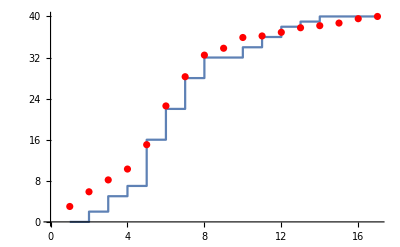

```mathematica
(* Plot data and model fit *)
gEmpirical=ListPlot[CummulativeFC,InterpolationOrder->0,Joined->True];
gFitted=ListPlot[HωList,PlotStyle->Red];(*,Joined->True,InterpolationOrder->4*)
Show[gEmpirical,gFitted]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Intervals=Table[i,{i,1,17}];Export["NB2_10cov_sim.xlsx",Transpose[{Intervals,FC,Cov1,Cov2,Cov3, Cov4, Cov5, Cov6, Cov7, Cov8, Cov9, Cov10}]]
```

C:\Users\Caroline\Desktop\covariate simulation\DS1\NB2